```mathematica
ПРИМЕР 1.
```

Латентные переменные. Измерить неизмеримое.
  Например, качество жизни.

-Graphics-

-Graphics-

ФАКТОРНЫЙ АНАЛИЗ
Метод  главных компонент

Исходные данные   Xi - вектор
i=7  количество объектов,  k=5 количество переменных

```mathematica
d={{68.9,1060 ,7.8,5.5,  25.3},{68.1,1101,9.5,15.3,28},{67.6,1147,10.1,30.2,30},{69.2,1204,10.0,44.5,23.50},
{69.2,1602,9.8,58.6,18},{64.6,1893,5.5,93.3,38.4},
{67.0,2777,6.2,122.0,29.6}};
%//MatrixForm
god={1970,1975,1980,1985,1990,1995,1998}
```

(68.9 | 1060 | 7.8 | 5.5 | 25.3
68.1 | 1101 | 9.5 | 15.3 | 28
67.6 | 1147 | 10.1 | 30.2 | 30
69.2 | 1204 | 10. | 44.5 | 23.5
69.2 | 1602 | 9.8 | 58.6 | 18
64.6 | 1893 | 5.5 | 93.3 | 38.4
67. | 2777 | 6.2 | 122. | 29.6)

{1970,1975,1980,1985,1990,1995,1998}

```mathematica
1.1. Расчет по формулам
```

Стандартизация
(можно не стандартизировать исходные переменные,
Mathematica делает по умолчанию)

```mathematica
dz=d//Standardize//N
{Mean[%]//Chop,Variance[%]}
```

{{0.670682,-0.768041,-0.319147,-1.12014,-0.354039},{0.182913,-0.702515,0.564073,-0.887921,0.0721609},{-0.121942,-0.628999,0.875798,-0.534851,0.387865},{0.853595,-0.537902,0.823844,-0.195999,-0.638173},{0.853595,0.098174,0.719935,0.138113,-1.50636},{-1.95107,0.563245,-1.51409,0.960362,1.71382},{-0.487769,1.97604,-1.15041,1.64044,0.324724}}

{{0,0,0,0,0},{1.,1.,1.,1.,1.}}

```mathematica
Mean[d]//N                                  (* среднее   *)
Sqrt[Variance[d]]//N           (* СКВО *)
```

{67.8,1540.57,8.41429,52.7714,27.5429}

{1.64012,625.711,1.92478,42.2013,6.33505}

Построим ковариационную матрицу для стандартизированной

```mathematica
dc=Covariance[dz];
%//MatrixForm
```

(1. | -0.50084 | 0.769223 | -0.595292 | -0.934048
-0.50084 | 1. | -0.700093 | 0.953664 | 0.296602
0.769223 | -0.700093 | 1. | -0.66918 | -0.680883
-0.595292 | 0.953664 | -0.66918 | 1. | 0.37011
-0.934048 | 0.296602 | -0.680883 | 0.37011 | 1.)

Построим корреляционную матрицу, совпадает с ковариационной, так как переменные стандартизированы

```mathematica
dc=Correlation[dz];
%//MatrixForm
```

(1. | -0.50084 | 0.769223 | -0.595292 | -0.934048
-0.50084 | 1. | -0.700093 | 0.953664 | 0.296602
0.769223 | -0.700093 | 1. | -0.66918 | -0.680883
-0.595292 | 0.953664 | -0.66918 | 1. | 0.37011
-0.934048 | 0.296602 | -0.680883 | 0.37011 | 1.)

```mathematica
dc=Covariance[dz];
%//MatrixForm
```

(1. | -0.50084 | 0.769223 | -0.595292 | -0.934048
-0.50084 | 1. | -0.700093 | 0.953664 | 0.296602
0.769223 | -0.700093 | 1. | -0.66918 | -0.680883
-0.595292 | 0.953664 | -0.66918 | 1. | 0.37011
-0.934048 | 0.296602 | -0.680883 | 0.37011 | 1.)

Найдем собственные числа, собственные векторы
ковариационной (корреляционной) матрицы

```mathematica
dval=Eigenvalues[dc]
dvec=Eigenvectors[dc];
%//MatrixForm
```

{3.60001,1.08999,0.244925,0.0465064,0.0185715}

(0.472291 | -0.42956 | 0.476894 | -0.446385 | -0.407102
-0.381124 | -0.539835 | -0.0428492 | -0.46524 | 0.5874
-0.297042 | 0.0326039 | 0.851618 | 0.380852 | 0.201004
0.499048 | 0.538495 | 0.167028 | -0.330656 | 0.568984
0.542589 | -0.482717 | -0.132609 | 0.574379 | 0.353673)

```mathematica
Total[dval]
```

5.

Собственные векторы  - по строкам  !!!

```mathematica
Eigensystem[dc]//MatrixForm
```

(3.60001 | 1.08999 | 0.244925 | 0.0465064 | 0.0185715
{0.472291,-0.42956,0.476894,-0.446385,-0.407102} | {-0.381124,-0.539835,-0.0428492,-0.46524,0.5874} | {-0.297042,0.0326039,0.851618,0.380852,0.201004} | {0.499048,0.538495,0.167028,-0.330656,0.568984} | {0.542589,-0.482717,-0.132609,0.574379,0.353673})

Cколько взять факторов?

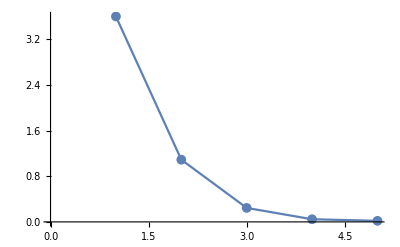

```mathematica
ListLinePlot[dval,PlotMarkers->{Automatic, 10}]
(* определение количества факторов графически  *)
```

Два собственных вектора > 1  
такое условие для отбора применяется в методе главных компонент

% дисперсии переменной объясненный фактором  
Объясненная суммарная дисперсия

```mathematica
dval/Total[dval]*100
Accumulate[dval]/Total[dval]* 100
```

{72.0002,21.7997,4.8985,0.930128,0.37143}

{72.0002,93.7999,98.6984,99.6286,100.}

Первый фактор объясняет 72% суммарной дисперсии
Второй фактор объясняет 21.8 % суммарной дисперсии

Не нормированные главные компоненты
Собственные векторы - матрица перехода 
(матрица вращения, так как исходные данные центрированы)
Матрица счетов (score) - старые переменные в новой системе координат

```mathematica
score=dz.Transpose[dvec];
%//MatrixForm
```

(1.13862 | 0.485849 | -0.993823 | 0.0367486 | 0.00837424
1.02414 | 0.740843 | 0.0794753 | 0.141853 | -0.12092
0.711112 | 0.825169 | 0.635822 | 0.144256 | -0.0487047
1.37439 | -0.353924 | 0.227587 | -0.024369 | 0.275275
1.2559 | -1.35826 | 0.112574 | -0.303661 | -0.133138
-3.01187 | 1.06432 | 0.0187283 | -0.265685 | 0.0280064
-2.49228 | -1.40399 | -0.0803633 | 0.270858 | -0.00889301)

Hормированные главные компоненты (факторы)
Главные компоненты

```mathematica
factors1=Table[score[[All,i]]/√dval[[i]],{i,1,Length[dval]}]//Transpose;
%//MatrixForm
```

(0.600105 | 0.465362 | -2.00813 | 0.170406 | 0.06145
0.539769 | 0.709603 | 0.160589 | 0.65778 | -0.887305
0.374788 | 0.790374 | 1.28475 | 0.668925 | -0.357394
0.724363 | -0.339 | 0.459865 | -0.113001 | 2.01996
0.661915 | -1.30099 | 0.227469 | -1.4081 | -0.976963
-1.58739 | 1.01944 | 0.0378427 | -1.232 | 0.20551
-1.31355 | -1.34479 | -0.162383 | 1.25599 | -0.0652567)

Матрица нагрузок

```mathematica
matr=Correlation[dz,score];
%//MatrixForm
```

(0.89611 | -0.397903 | -0.147006 | 0.107621 | 0.0739427
-0.815034 | -0.563601 | 0.0161356 | 0.116128 | -0.0657835
0.904844 | -0.0447356 | 0.421464 | 0.0360203 | -0.0180717
-0.846958 | -0.485721 | 0.188483 | -0.0713071 | 0.0782748
-0.772424 | 0.613259 | 0.0994764 | 0.122703 | 0.0481976)

-Graphics-

С первым фактором сильно коррелируют все переменные 
(L+,M-,P+,A-,V-)
переменные M-,V+ относятся к двум факторам одновременно.
Первый фактор можно рассматривать, как признак благополучия
Чем больше фактор, тем благополучнее год

Оставим два  фактора, для которых с.ч. > 1
Перейдем к факторам

С первым фактором сильно коррелируют все переменные 
(L+,M-,P+,A-,V-)
переменные M-,V+ относятся к двум факторам одновременно.
Первый фактор можно рассматривать, как признак благополучия
Чем больше фактор, тем благополучнее год

Оставим два  фактора, для которых с.ч. > 1
Перейдем к факторам

```mathematica
factors1//Grid  (* факторы, новые переменные *)
```

0.600105 | 0.465362 | -2.00813 | 0.170406 | 0.06145
0.539769 | 0.709603 | 0.160589 | 0.65778 | -0.887305
0.374788 | 0.790374 | 1.28475 | 0.668925 | -0.357394
0.724363 | -0.339 | 0.459865 | -0.113001 | 2.01996
0.661915 | -1.30099 | 0.227469 | -1.4081 | -0.976963
-1.58739 | 1.01944 | 0.0378427 | -1.232 | 0.20551
-1.31355 | -1.34479 | -0.162383 | 1.25599 | -0.0652567

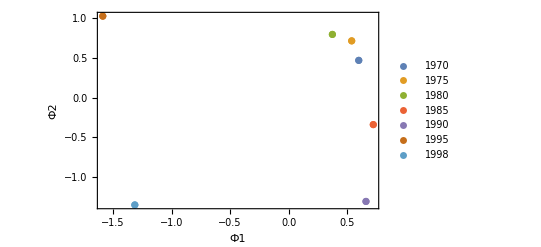

```mathematica
g=god//ToString;
ListPlot[Table[{{factors1[[i,1]],factors1[[i,2]]}},{i,1,7}],Frame->True,PlotLegends->god,FrameLabel->{"Ф1","Ф2"}]
```

Чем больше первый фактор, тем лучше год